## Bac Transition

(0.00461625+0.000845255 ⅈ | 0.+0. ⅈ | -0.584529+0.811359 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.000378936+0.000525984 ⅈ | 0.+0. ⅈ | -5.24798×10^-12+4.13399×10^-11 ⅈ
0.+0. ⅈ | 0.00463162-0.000615312 ⅈ | 0.+0. ⅈ | -0.0994538+0.995033 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.13445+0.990909 ⅈ | 0.+0. ⅈ | 0.00447166+0.00142426 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 2.46108×10^-6+1.65286×10^-6 ⅈ | 0.+0. ⅈ | -0.000167365-0.000626299 ⅈ
0.+0. ⅈ | 0.611742+0.791045 ⅈ | 0.+0. ⅈ | 0.00425362-0.00193318 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.00517311-0.00328034 ⅈ | 0.+0. ⅈ | 0.344395+0.938805 ⅈ | 0.+0. ⅈ
0.0000871609+0.000642382 ⅈ | 0.+0. ⅈ | 2.46108×10^-6+1.65286×10^-6 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.000675319-0.00112542 ⅈ | 0.+0. ⅈ | 0.25817+0.9661 ⅈ
0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.607316+0.794437 ⅈ | 0.+0. ⅈ | 0.00396757+0.00466692 ⅈ | 0.+0. ⅈ
1.20113×10^-11+3.33024×10^-11 ⅈ | 0.+0. ⅈ | -0.0000757734-0.000643832 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.116885+0.993146 ⅈ | 0.+0. ⅈ | 0.00104322+0.000796448 ⅈ)

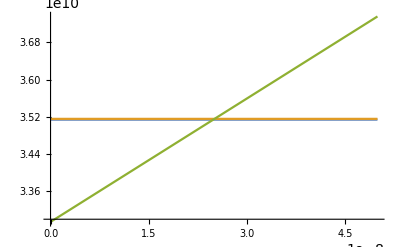

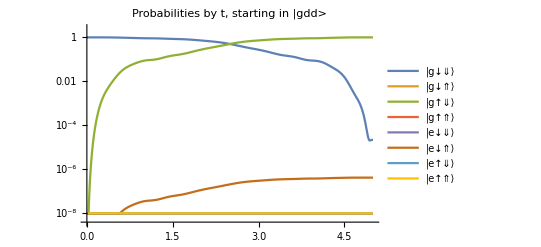

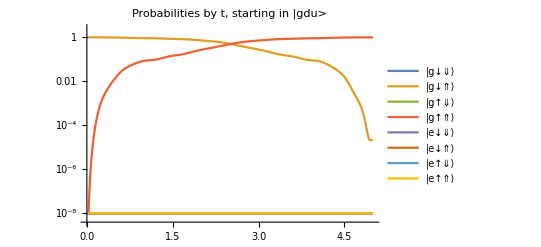

```mathematica
setVariables[]

T1 = 10*10^-9;
T2 = 30*10^-9;
Tmax = 2*T1 + T2;

ΔE = 5000;

Ea =0;
ωE = 2*π*ϵ0;

(*BaD = EaD*(d*e)/(γe*h);*)
Ba = .01;
ωB = 2*π*(B0*γe - 3*A + 6*A*t/Tmax);

(*fidelityToGate[EaD, BaD, ωED, ωBD, "XY"]*)
Clear[Eamp, Bamp];
Eamp[t_] := Ea*cosWindow[t, T1, Tmax];
Bamp[t_] := Ba*cosWindow[t, T1, Tmax];

U = findEvolutionOperator[Hcorrected, Tmax];

(U /. t->Tmax) // MatrixForm


Plot[{δLab[1, 3], δLab[2, 4], ωB}, {t, 0, Tmax}, PlotRange->All]

Evaluate@Table[Max[Abs[U[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>"]

Evaluate@Table[Max[Abs[U[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>"]


clearVariables[]
```

## ΔE Sweep, nonadiabatic

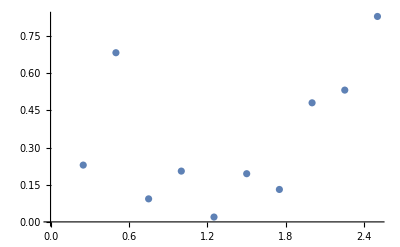

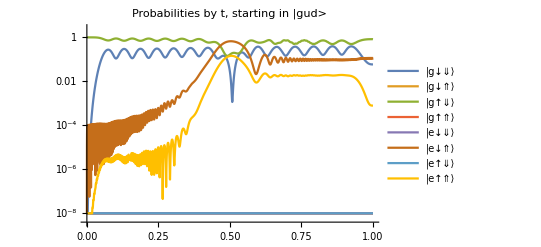

```mathematica
setVariables[]

Clear[bumpError];
bumpError[dtdΔE_] := (

ΔE0 = 2000;

Tmax = 2*ΔE0*dtdΔE;
T1 = Tmax/10;
(*Tmax = 50*10^-9;*)

ΔE = ΔE0 - 2*ΔE0*(t/Tmax)(* + 0*Sin[t*4/(5*10^-9)]*);

Ea =0;
ωE = ωB;

Ba = .01;
ωB = 2*π*(B0*γe - A);

(*Plot[{δLab[3, 6]}, {t, 0, Tmax}]*)

Clear[Eamp, Bamp];
Eamp[t_] := Ea*cosWindow[t, T1, Tmax];
Bamp[t_] := Ba*cosWindow[t, T1, Tmax];

U = findEvolutionOperator[Hcorrected, Tmax];

error = Abs[U[[3, 3]]]^2 /. t->Tmax;

error

)

rates = Table[(ξ*100*10^-9)/4000, {ξ, .1, 1, .1}];
errors = Table[bumpError[r], {r, rates}];

ListPlot[Transpose[{rates, errors}]]

Evaluate@Table[Max[Abs[U[[i]][[3]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gud>"]


clearVariables[]
```

```mathematica
Transpose[{rates, errors}] // MatrixForm
```

(2.5×10^-12 | 0.872325
5.×10^-12 | 0.719618
7.5×10^-12 | 0.616299
1.×10^-11 | 0.549667
1.25×10^-11 | 0.523276
1.5×10^-11 | 0.526488
1.75×10^-11 | 0.574234
2.×10^-11 | 0.604147
2.25×10^-11 | 0.669837
2.5×10^-11 | 0.723304)

```mathematica
Transpose[{rates, errors}] // MatrixForm
```

(2.5×10^-12 | 0.857228
5.×10^-12 | 0.694105
7.5×10^-12 | 0.607107
1.×10^-11 | 0.538884
1.25×10^-11 | 0.496131
1.5×10^-11 | 0.511265
1.75×10^-11 | 0.558873
2.×10^-11 | 0.579211
2.25×10^-11 | 0.650305
2.5×10^-11 | 0.707847)

## ΔE Sweep, Adiabatic

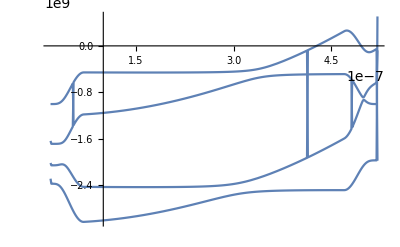

( | |g↓⇓⟩ | |g↓⇑⟩ | |g↑⇓⟩ | |g↑⇑⟩ | |e↓⇓⟩ | |e↓⇑⟩ | |e↑⇓⟩ | |e↑⇑⟩
|g↓⇓⟩ | -0.0144885-0.0084442 ⅈ | 0.+0. ⅈ | -0.17776+0.346209 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.873402-0.291017 ⅈ | 0.+0. ⅈ | 0.0229855-0.0144744 ⅈ
|g↓⇑⟩ | 0.+0. ⅈ | -0.637659+0.770171 ⅈ | 0.+0. ⅈ | 0.0148643+0.00255057 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
|g↑⇓⟩ | 0.000418893-0.00749562 ⅈ | 0.+0. ⅈ | -0.0454601-0.0485654 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0287462-0.025362 ⅈ | 0.+0. ⅈ | 0.94083-0.329983 ⅈ
|g↑⇑⟩ | 0.+0. ⅈ | -0.01116+0.0101443 ⅈ | 0.+0. ⅈ | -0.951791-0.306376 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ
|e↓⇓⟩ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.983787+0.179257 ⅈ | 0.+0. ⅈ | 0.00410148+0.00383914 ⅈ | 0.+0. ⅈ
|e↓⇑⟩ | 0.259071-0.965623 ⅈ | 0.+0. ⅈ | 0.00761012+0.0117209 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.0110478-0.0093499 ⅈ | 0.+0. ⅈ | -0.00706436+0.00102928 ⅈ
|e↑⇓⟩ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.00392562+0.00401879 ⅈ | 0.+0. ⅈ | -0.990821-0.135065 ⅈ | 0.+0. ⅈ
|e↑⇑⟩ | 0.00125177+0.0107974 ⅈ | 0.+0. ⅈ | 0.419534+0.817259 ⅈ | 0.+0. ⅈ | 0.+0. ⅈ | -0.116806+0.370345 ⅈ | 0.+0. ⅈ | 0.0714869+0.00720945 ⅈ)

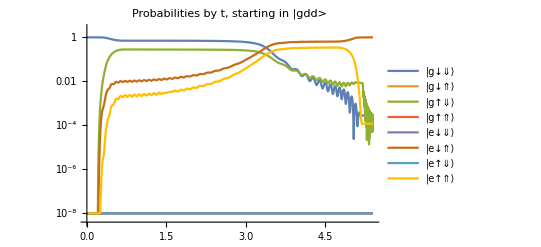

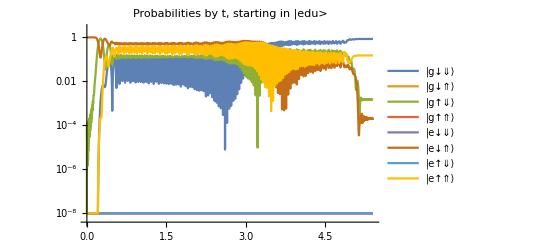

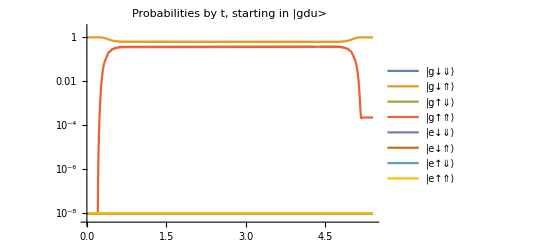

```mathematica
setVariables[]


ΔE0 = 2000;
ΔE1 = 500;

T0 = 20*10^-9;
Tsweep = 500*10^-9;
T1 = Tsweep/10;
T2 = 20*10^-9;
Tmax = T0 + Tsweep + T2;

ΔE = Piecewise[{{ΔE0 - ΔE0*t/T0, t ≤ T0}, {-ΔE1*(t - T0)/(Tsweep), T0 < t ≤ T0 + Tsweep}, {-ΔE1 - (ΔE0 - ΔE1)*(t - T0 - Tsweep)/(T2), T0 + Tsweep < t}}] + .5;
(*ΔE = ΔE /. t->(Tmax - t);*)

Ea =0;
ωE = ωB;

Ba = .02;
ωB = 2*π*(B0*γe + A/2) + 3*10^8;

(*Plot[{δLab[3, 6]}, {t, 0, Tmax}]*)

Clear[Eamp, Bamp];
Eamp[t_] := Ea*cosWindow[t, T1, Tmax];
Bamp[t_] := Ba*cosWindow[t - T0, T1, Tsweep];

(*Plot[ΔE, {t, 0, Tmax}, PlotRange->All]
Plot[Bamp[t], {t, 0, Tmax}, PlotRange->All]*)

relevantSubspace = Hcorrected[[{1, 3, 6, 8}, {1, 3, 6, 8}]];

Plot[Eigenvalues[relevantSubspace /. t->tt] - 10^9, {tt, T0 - 10^-9, T0 + Tsweep + 10^-9}, PlotRange->All, MaxRecursion->3]

U = findEvolutionOperator[Hcorrected, Tmax];

ϕ1 = complexPhase[U[[1, 6]] /. t->Tmax];
ϕ0 = complexPhase[U[[2, 2]] /. t->Tmax];
Δϕ = ϕ1 - ϕ0;

printWithBasis[U /. t->Tmax, basisGE]

Evaluate@Table[Max[Abs[U[[i]][[1]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdd>", PlotRange->All]
Evaluate@Table[Max[Abs[U[[i]][[6]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |edu>", PlotRange->All]
Evaluate@Table[Max[Abs[U[[i]][[2]]]^2, 10^-8], {i, 8}];
LogPlot[{%[[1]], %[[2]], %[[3]], %[[4]], %[[5]], %[[6]], %[[7]], %[[8]]}, {t, 0,  Tmax}, PlotLegends->basisGE, PlotLabel->"Probabilities by t, starting in |gdu>", PlotRange->All]


clearVariables[]
```

```mathematica
Δϕ
```

-2.85802

```mathematica
Δϕ
```

-2.58398

```mathematica
setVariables[]

ωB = 2*π*(B0*γe + A/2) + 1*10^8;

δRot[1, 3]
δRot[2, 4]

clearVariables[]
```

-6.86498×10^8

-3.18931×10^8

```mathematica
setVariables[]

ΔE = 1000;
statesInOrder[HexactStatic] // MatrixForm

clearVariables[]
```

(0.999998 | -5.20229×10^-19 | -3.73288×10^-18 | 0. | 0.00218588 | 4.97811×10^-20 | 0. | 0.
7.43643×10^-19 | 0.999994 | -0.0023969 | 0. | 0. | -0.00151358 | 0.00201296 | 0.
-7.35836×10^-18 | -0.00243605 | -0.999726 | 0. | 1.83187×10^-15 | -0.0231711 | 0.00234587 | 0.
0. | 0. | 0. | 0.999999 | 0. | 0. | 0. | 0.00148537
-0.00218588 | 1.63736×10^-16 | 1.72406×10^-15 | 0. | 0.999998 | -7.21743×10^-16 | 0. | 0.
-2.15524×10^-18 | 0.00147367 | -0.0231928 | 0. | 6.66134×10^-16 | 0.999698 | -0.00801043 | 0.
1.49964×10^-21 | 0.0019955 | -0.00216435 | 0. | -1.73472×10^-18 | -0.00806571 | -0.999963 | 0.
0. | 0. | 0. | -0.00148537 | 0. | 0. | 0. | 0.999999)

## ΔE Sweep, adiabatic, with two qubits